```mathematica
Clear[x,y,H0b,Hb,Hyy,Hy,Ha,H0a,F0,Fab,m,n,h,a,b,H,d,σ,μ0]
Hyy=Integrate[(σ/(4π μ0))(n-y)/((x-m)^2+(y-n)^2+h^2)^(3/2),y];
TraditionalForm[FullSimplify[Hyy]]
```

σ/(4 π μ0 √(h^2+(m-x)^2+(n-y)^2))

```mathematica
σ/(4 π μ0 √(h^2+(m-x)^2+(n-y)^2))
```

```mathematica
y=0;
H0b=Hyy;
y=b;
Hb=Hyy;
Hyb=Hb-H0b;
TraditionalForm[FullSimplify[Hyb]]
```

(σ (1/(√((b-n)^2+h^2+(m-x)^2))-1/(√(h^2+(m-x)^2+n^2))))/(4 π μ0)

```mathematica
Hyx=Integrate[Hyb,x]
```

1/(4 π μ0)σ (-Log[-m+x+√(h^2+m^2+n^2-2 m x+x^2)]+Log[-m+x+√(b^2+h^2+m^2-2 b n+n^2-2 m x+x^2)])

```mathematica
x=0;
H0a=Hyx;
x=a;
Ha=Hyx;
Hy=Ha-H0a;
TraditionalForm[FullSimplify[Hy]]
```

1/(4 π μ0)σ (log(√((a-m)^2+(b-n)^2+h^2)+a-m)-log(√((a-m)^2+h^2+n^2)+a-m)-log(√((b-n)^2+h^2+m^2)-m)+log(√(h^2+m^2+n^2)-m))

-Graphics3D-

{{0.,-2.19973×10^-9},{0.1,935716.},{0.2,1.8711×10^6},{0.3,2.80582×10^6},{0.4,3.73954×10^6},{0.5,4.67194×10^6},{0.6,5.60269×10^6},{0.7,6.53147×10^6},{0.8,7.45797×10^6},{0.9,8.38187×10^6},{1.,9.30287×10^6},{1.1,1.02207×10^7},{1.2,1.1135×10^7},{1.3,1.20455×10^7},{1.4,1.2952×10^7},{1.5,1.38542×10^7},{1.6,1.47518×10^7},{1.7,1.56446×10^7},{1.8,1.65323×10^7},{1.9,1.74147×10^7},{2.,1.82916×10^7},{2.1,1.91628×10^7},{2.2,2.00281×10^7},{2.3,2.08872×10^7},{2.4,2.17401×10^7},{2.5,2.25865×10^7},{2.6,2.34263×10^7},{2.7,2.42593×10^7},{2.8,2.50854×10^7},{2.9,2.59044×10^7},{3.,2.67171×10^7},{3.1,2.75207×10^7},{3.2,2.83179×10^7},{3.3,2.91075×10^7},{3.4,2.98895×10^7},{3.5,3.06639×10^7},{3.6,3.14304×10^7},{3.7,3.21892×10^7},{3.8,3.294×10^7},{3.9,3.36829×10^7},{4.,3.44178×10^7},{4.1,3.51446×10^7},{4.2,3.58634×10^7},{4.3,3.6574×10^7},{4.4,3.72764×10^7},{4.5,3.79707×10^7},{4.6,3.86567×10^7},{4.7,3.93345×10^7},{4.8,4.00041×10^7},{4.9,4.06655×10^7},{5.,4.13185×10^7}}

InterpolatingFunction[…]

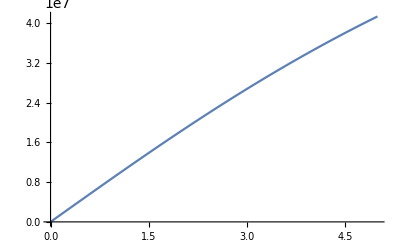

{{0.,-2.19973×10^-9},{0.1,935716.},{0.2,1.8711×10^6},{0.3,2.80582×10^6},{0.4,3.73954×10^6},{0.5,4.67194×10^6},{0.6,5.60269×10^6},{0.7,6.53147×10^6},{0.8,7.45797×10^6},{0.9,8.38187×10^6},{1.,9.30287×10^6},{1.1,1.02207×10^7},{1.2,1.1135×10^7},{1.3,1.20455×10^7},{1.4,1.2952×10^7},{1.5,1.38542×10^7},{1.6,1.47518×10^7},{1.7,1.56446×10^7},{1.8,1.65323×10^7},{1.9,1.74147×10^7},{2.,1.82916×10^7},{2.1,1.91628×10^7},{2.2,2.00281×10^7},{2.3,2.08872×10^7},{2.4,2.17401×10^7},{2.5,2.25865×10^7},{2.6,2.34263×10^7},{2.7,2.42593×10^7},{2.8,2.50854×10^7},{2.9,2.59044×10^7},{3.,2.67171×10^7},{3.1,2.75207×10^7},{3.2,2.83179×10^7},{3.3,2.91075×10^7},{3.4,2.98895×10^7},{3.5,3.06639×10^7},{3.6,3.14304×10^7},{3.7,3.21892×10^7},{3.8,3.294×10^7},{3.9,3.36829×10^7},{4.,3.44178×10^7},{4.1,3.51446×10^7},{4.2,3.58634×10^7},{4.3,3.6574×10^7},{4.4,3.72764×10^7},{4.5,3.79707×10^7},{4.6,3.86567×10^7},{4.7,3.93345×10^7},{4.8,4.00041×10^7},{4.9,4.06655×10^7},{5.,4.13185×10^7}}

InterpolatingFunction[…]

-Graphics-

```mathematica
Clear[m,n]
a=30;
b=20;
h=5;
σ=1.23;
μ0=4π 10^-7;
Plot3D[σ/(4 π μ0)(log(√((a-m)^2+(b-n)^2+h^2)+a-m)-log(√((a-m)^2+h^2+n^2)+a-m)-log(√((b-n)^2+h^2+m^2)-m)+log(√(h^2+m^2+n^2)-m)),{m,0,30},{n,0,20}]

T=Table[{d,NIntegrate[σ/(4 π μ0)(log(√((a-m)^2+(b-n)^2+h^2)+a-m)-log(√((a-m)^2+h^2+n^2)+a-m)-log(√((b-n)^2+h^2+m^2)-m)+log(√(h^2+m^2+n^2)-m)),{m,0,a},{n,0+d,b+d}]},{d,0,5,0.1}]
f=Interpolation[T]
Plot[f[x],{x,0,5}]
```

```mathematica
ff=Integrate[σ/(4 π μ0)(log(√((a-m)^2+(b-n)^2+h^2)+a-m)-log(√((a-m)^2+h^2+n^2)+a-m)-log(√((b-n)^2+h^2+m^2)-m)+log(√(h^2+m^2+n^2)-m)),n]
n=d+b
ff
```

1/(4 π μ0)σ (h ArcTan[(m (b-n))/(h √(h^2+m^2+(b-n)^2))]-((-a h^2+h^2 m) ArcTan[((a-m) (b-n))/(h √(a^2+h^2-2 a m+m^2+(b-n)^2))])/(h (a-m))+h ArcTan[(m n)/(h √(h^2+m^2+n^2))]-((-a h^2+h^2 m) ArcTan[((a-m) n)/(h √(a^2+h^2-2 a m+m^2+n^2))])/(h (a-m))+(b-n) Log[-m+√(h^2+m^2+(b-n)^2)]-(b-n) Log[a-m+√(a^2+h^2-2 a m+m^2+(b-n)^2)]-m Log[b+√(h^2+m^2+(b-n)^2)-n]-(a-m) Log[b+√(a^2+h^2-2 a m+m^2+(b-n)^2)-n]+n Log[-m+√(h^2+m^2+n^2)]-m Log[n+√(h^2+m^2+n^2)]-n Log[a-m+√(a^2+h^2-2 a m+m^2+n^2)]-(a-m) Log[n+√(a^2+h^2-2 a m+m^2+n^2)])

b+d

1/(4 π μ0)σ (-h ArcTan[(d m)/(h √(d^2+h^2+m^2))]+h ArcTan[((b+d) m)/(h √((b+d)^2+h^2+m^2))]+((-a h^2+h^2 m) ArcTan[(d (a-m))/(h √(a^2+d^2+h^2-2 a m+m^2))])/(h (a-m))-((-a h^2+h^2 m) ArcTan[((b+d) (a-m))/(h √(a^2+(b+d)^2+h^2-2 a m+m^2))])/(h (a-m))-m Log[-d+√(d^2+h^2+m^2)]-d Log[-m+√(d^2+h^2+m^2)]-m Log[b+d+√((b+d)^2+h^2+m^2)]+(b+d) Log[-m+√((b+d)^2+h^2+m^2)]-(a-m) Log[-d+√(a^2+d^2+h^2-2 a m+m^2)]+d Log[a-m+√(a^2+d^2+h^2-2 a m+m^2)]-(a-m) Log[b+d+√(a^2+(b+d)^2+h^2-2 a m+m^2)]-(b+d) Log[a-m+√(a^2+(b+d)^2+h^2-2 a m+m^2)])

```mathematica
1/(4 π μ0)σ (-h ArcTan[(d m)/(h √(d^2+h^2+m^2))]+h ArcTan[((b+d) m)/(h √((b+d)^2+h^2+m^2))]+((-a h^2+h^2 m) ArcTan[(d (a-m))/(h √(a^2+d^2+h^2-2 a m+m^2))])/(h (a-m))-((-a h^2+h^2 m) ArcTan[((b+d) (a-m))/(h √(a^2+(b+d)^2+h^2-2 a m+m^2))])/(h (a-m))-m Log[-d+√(d^2+h^2+m^2)]-d Log[-m+√(d^2+h^2+m^2)]-m Log[b+d+√((b+d)^2+h^2+m^2)]+(b+d) Log[-m+√((b+d)^2+h^2+m^2)]-(a-m) Log[-d+√(a^2+d^2+h^2-2 a m+m^2)]+d Log[a-m+√(a^2+d^2+h^2-2 a m+m^2)]-(a-m) Log[b+d+√(a^2+(b+d)^2+h^2-2 a m+m^2)]-(b+d) Log[a-m+√(a^2+(b+d)^2+h^2-2 a m+m^2)])-1/(4 π μ0)σ (h ArcTan[((b-d) m)/(h √((b-d)^2+h^2+m^2))]+h ArcTan[(d m)/(h √(d^2+h^2+m^2))]-((-a h^2+h^2 m) ArcTan[((b-d) (a-m))/(h √(a^2+(b-d)^2+h^2-2 a m+m^2))])/(h (a-m))-((-a h^2+h^2 m) ArcTan[(d (a-m))/(h √(a^2+d^2+h^2-2 a m+m^2))])/(h (a-m))-m Log[b-d+√((b-d)^2+h^2+m^2)]+(b-d) Log[-m+√((b-d)^2+h^2+m^2)]-m Log[d+√(d^2+h^2+m^2)]+d Log[-m+√(d^2+h^2+m^2)]-(a-m) Log[b-d+√(a^2+(b-d)^2+h^2-2 a m+m^2)]-(b-d) Log[a-m+√(a^2+(b-d)^2+h^2-2 a m+m^2)]-(a-m) Log[d+√(a^2+d^2+h^2-2 a m+m^2)]-d Log[a-m+√(a^2+d^2+h^2-2 a m+m^2)])
```

-1/(4 π μ0)σ (h ArcTan[((b-d) m)/(h √((b-d)^2+h^2+m^2))]+h ArcTan[(d m)/(h √(d^2+h^2+m^2))]-((-a h^2+h^2 m) ArcTan[((b-d) (a-m))/(h √(a^2+(b-d)^2+h^2-2 a m+m^2))])/(h (a-m))-((-a h^2+h^2 m) ArcTan[(d (a-m))/(h √(a^2+d^2+h^2-2 a m+m^2))])/(h (a-m))-m Log[b-d+√((b-d)^2+h^2+m^2)]+(b-d) Log[-m+√((b-d)^2+h^2+m^2)]-m Log[d+√(d^2+h^2+m^2)]+d Log[-m+√(d^2+h^2+m^2)]-(a-m) Log[b-d+√(a^2+(b-d)^2+h^2-2 a m+m^2)]-(b-d) Log[a-m+√(a^2+(b-d)^2+h^2-2 a m+m^2)]-(a-m) Log[d+√(a^2+d^2+h^2-2 a m+m^2)]-d Log[a-m+√(a^2+d^2+h^2-2 a m+m^2)])+1/(4 π μ0)σ (-h ArcTan[(d m)/(h √(d^2+h^2+m^2))]+h ArcTan[((b+d) m)/(h √((b+d)^2+h^2+m^2))]+((-a h^2+h^2 m) ArcTan[(d (a-m))/(h √(a^2+d^2+h^2-2 a m+m^2))])/(h (a-m))-((-a h^2+h^2 m) ArcTan[((b+d) (a-m))/(h √(a^2+(b+d)^2+h^2-2 a m+m^2))])/(h (a-m))-m Log[-d+√(d^2+h^2+m^2)]-d Log[-m+√(d^2+h^2+m^2)]-m Log[b+d+√((b+d)^2+h^2+m^2)]+(b+d) Log[-m+√((b+d)^2+h^2+m^2)]-(a-m) Log[-d+√(a^2+d^2+h^2-2 a m+m^2)]+d Log[a-m+√(a^2+d^2+h^2-2 a m+m^2)]-(a-m) Log[b+d+√(a^2+(b+d)^2+h^2-2 a m+m^2)]-(b+d) Log[a-m+√(a^2+(b+d)^2+h^2-2 a m+m^2)])

```mathematica
FullSimplify[%]
```

1/(4 π μ0)(-σ (h (ArcTan[((b-d) (a-m))/(h √((b-d)^2+h^2+(a-m)^2))]+2 ArcTan[(d (a-m))/(h √(d^2+h^2+(a-m)^2))]-ArcTan[((b+d) (a-m))/(h √((b+d)^2+h^2+(a-m)^2))]+ArcTan[((b-d) m)/(h √((b-d)^2+h^2+m^2))]+2 ArcTan[(d m)/(h √(d^2+h^2+m^2))]-ArcTan[((b+d) m)/(h √((b+d)^2+h^2+m^2))])+(-a+m) Log[b-d+√((b-d)^2+h^2+(a-m)^2)]+(a-m) Log[-d+√(d^2+h^2+(a-m)^2)]-a Log[d+√(d^2+h^2+(a-m)^2)]+m Log[d+√(d^2+h^2+(a-m)^2)]+a Log[b+d+√((b+d)^2+h^2+(a-m)^2)]-m Log[b+d+√((b+d)^2+h^2+(a-m)^2)]+(-b+d) Log[a+√((b-d)^2+h^2+(a-m)^2)-m]-m Log[b-d+√((b-d)^2+h^2+m^2)]+b (Log[a+√((b+d)^2+h^2+(a-m)^2)-m]+Log[-m+√((b-d)^2+h^2+m^2)])+m Log[-d+√(d^2+h^2+m^2)]-m Log[d+√(d^2+h^2+m^2)]+d (-2 Log[a+√(d^2+h^2+(a-m)^2)-m]+Log[a+√((b+d)^2+h^2+(a-m)^2)-m]-Log[-m+√((b-d)^2+h^2+m^2)]+2 Log[-m+√(d^2+h^2+m^2)])+m Log[b+d+√((b+d)^2+h^2+m^2)])+(b+d) σ Log[-m+√((b+d)^2+h^2+m^2)])

```mathematica
fm=Integrate[1/(4 π μ0)(-σ (h (ArcTan[((b-d) (a-m))/(h √((b-d)^2+h^2+(a-m)^2))]+2 ArcTan[(d (a-m))/(h √(d^2+h^2+(a-m)^2))]-ArcTan[((b+d) (a-m))/(h √((b+d)^2+h^2+(a-m)^2))]+ArcTan[((b-d) m)/(h √((b-d)^2+h^2+m^2))]+2 ArcTan[(d m)/(h √(d^2+h^2+m^2))]-ArcTan[((b+d) m)/(h √((b+d)^2+h^2+m^2))])+(-a+m) Log[b-d+√((b-d)^2+h^2+(a-m)^2)]+(a-m) Log[-d+√(d^2+h^2+(a-m)^2)]-a Log[d+√(d^2+h^2+(a-m)^2)]+m Log[d+√(d^2+h^2+(a-m)^2)]+a Log[b+d+√((b+d)^2+h^2+(a-m)^2)]-m Log[b+d+√((b+d)^2+h^2+(a-m)^2)]+(-b+d) Log[a+√((b-d)^2+h^2+(a-m)^2)-m]-m Log[b-d+√((b-d)^2+h^2+m^2)]+b (Log[a+√((b+d)^2+h^2+(a-m)^2)-m]+Log[-m+√((b-d)^2+h^2+m^2)])+m Log[-d+√(d^2+h^2+m^2)]-m Log[d+√(d^2+h^2+m^2)]+d (-2 Log[a+√(d^2+h^2+(a-m)^2)-m]+Log[a+√((b+d)^2+h^2+(a-m)^2)-m]-Log[-m+√((b-d)^2+h^2+m^2)]+2 Log[-m+√(d^2+h^2+m^2)])+m Log[b+d+√((b+d)^2+h^2+m^2)])+(b+d) σ Log[-m+√((b+d)^2+h^2+m^2)]),m]
m=a
fm
```

1/(4 π μ0)(-d √(d^2+h^2+m^2) σ-1/2 (b-d) √(b^2-2 b d+d^2+h^2+m^2) σ+1/2 (b+d) √(b^2+2 b d+d^2+h^2+m^2) σ+d √(a^2+d^2+h^2-2 a m+m^2) σ-1/2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2) σ-1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2) σ-2 h m σ ArcTan[(d m)/(h √(d^2+h^2+m^2))]-h m σ ArcTan[((b-d) m)/(h √(b^2-2 b d+d^2+h^2+m^2))]+h m σ ArcTan[((b+d) m)/(h √(b^2+2 b d+d^2+h^2+m^2))]-2 h m σ ArcTan[(d (a-m))/(h √(a^2+d^2+h^2-2 a m+m^2))]-h m σ ArcTan[((b-d) (a-m))/(h √(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2))]+h m σ ArcTan[((b+d) (a-m))/(h √(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2))]-1/2 m^2 σ Log[-d+√(d^2+h^2+m^2)]+1/2 m^2 σ Log[d+√(d^2+h^2+m^2)]-2 d m σ Log[-m+√(d^2+h^2+m^2)]-1/2 h^2 σ Log[-(4 ⅈ (-ⅈ d^2-ⅈ h^2+h m))/(d^2 h^2 (-ⅈ h+m))-(4 √(d^2+h^2+m^2))/(d h^2 (-ⅈ h+m))]-1/2 h^2 σ Log[(4 ⅈ (ⅈ d^2+ⅈ h^2+h m))/(d^2 h^2 (ⅈ h+m))-(4 √(d^2+h^2+m^2))/(d h^2 (ⅈ h+m))]+1/2 m^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2+m^2)]-(b-d) m σ Log[-m+√(b^2-2 b d+d^2+h^2+m^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2-h^2-ⅈ h m))/((b-d)^2 h^2 (-ⅈ h+m))-(8 √(b^2-2 b d+d^2+h^2+m^2))/((b-d) h^2 (-ⅈ h+m))]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2-h^2+ⅈ h m))/((b-d)^2 h^2 (ⅈ h+m))-(8 √(b^2-2 b d+d^2+h^2+m^2))/((b-d) h^2 (ⅈ h+m))]-1/2 m^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2+m^2)]+(b+d) m σ Log[-m+√(b^2+2 b d+d^2+h^2+m^2)]+1/4 h^2 σ Log[(8 (b^2+2 b d+d^2+h^2+ⅈ h m))/((b+d)^2 h^2 (-ⅈ h+m))+(8 √(b^2+2 b d+d^2+h^2+m^2))/((b+d) h^2 (-ⅈ h+m))]+1/4 h^2 σ Log[(8 (b^2+2 b d+d^2+h^2-ⅈ h m))/((b+d)^2 h^2 (ⅈ h+m))+(8 √(b^2+2 b d+d^2+h^2+m^2))/((b+d) h^2 (ⅈ h+m))]+1/2 m (-2 a+m) σ Log[-d+√(a^2+d^2+h^2-2 a m+m^2)]-1/2 m (-2 a+m) σ Log[d+√(a^2+d^2+h^2-2 a m+m^2)]+2 d m σ Log[a-m+√(a^2+d^2+h^2-2 a m+m^2)]+2 a d σ Log[-a+m+√(a^2+d^2+h^2-2 a m+m^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 (d^2-ⅈ a h+h^2+ⅈ h m))/(d^2 (-ⅈ a+h)^2 (-a-ⅈ h+m))+(4 √(a^2+d^2+h^2-2 a m+m^2))/(d (-ⅈ a+h)^2 (-a-ⅈ h+m))]+1/2 (ⅈ a+h)^2 σ Log[(4 (d^2+ⅈ a h+h^2-ⅈ h m))/(d^2 (ⅈ a+h)^2 (-a+ⅈ h+m))+(4 √(a^2+d^2+h^2-2 a m+m^2))/(d (ⅈ a+h)^2 (-a+ⅈ h+m))]-1/2 m (-2 a+m) σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2)]+(b-d) m σ Log[a-m+√(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2)]+a (b-d) σ Log[-a+m+√(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 (b^2-2 b d+d^2-ⅈ a h+h^2+ⅈ h m))/((b-d)^2 (-ⅈ a+h)^2 (-a-ⅈ h+m))+(8 √(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2))/((b-d) (-ⅈ a+h)^2 (-a-ⅈ h+m))]+1/4 (ⅈ a+h)^2 σ Log[(8 (b^2-2 b d+d^2+ⅈ a h+h^2-ⅈ h m))/((b-d)^2 (ⅈ a+h)^2 (-a+ⅈ h+m))+(8 √(a^2+b^2-2 b d+d^2+h^2-2 a m+m^2))/((b-d) (ⅈ a+h)^2 (-a+ⅈ h+m))]+1/2 m (-2 a+m) σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2)]-(b+d) m σ Log[a-m+√(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2)]-a (b+d) σ Log[-a+m+√(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 (b^2+2 b d+d^2-ⅈ a h+h^2+ⅈ h m))/((b+d)^2 (-ⅈ a+h)^2 (-a-ⅈ h+m))-(8 √(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2))/((b+d) (-ⅈ a+h)^2 (-a-ⅈ h+m))]-1/4 (ⅈ a+h)^2 σ Log[-(8 (b^2+2 b d+d^2+ⅈ a h+h^2-ⅈ h m))/((b+d)^2 (ⅈ a+h)^2 (-a+ⅈ h+m))-(8 √(a^2+b^2+2 b d+d^2+h^2-2 a m+m^2))/((b+d) (ⅈ a+h)^2 (-a+ⅈ h+m))])

a

```mathematica
1/(4 π μ0)(d √(d^2+h^2) σ-d √(a^2+d^2+h^2) σ-1/2 (-b+d) √(b^2-2 b d+d^2+h^2) σ-1/2 (b-d) √(a^2+b^2-2 b d+d^2+h^2) σ-1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ+1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-2 a h σ ArcTan[(a d)/(h √(a^2+d^2+h^2))]-a h σ ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+a h σ ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+4 a d σ Log[√(d^2+h^2)]+2 a (b-d) σ Log[√(b^2-2 b d+d^2+h^2)]-2 a (b+d) σ Log[√(b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[-d+√(d^2+h^2)]+1/2 a^2 σ Log[d+√(d^2+h^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 ⅈ √(d^2+h^2))/(d h (-ⅈ a+h)^2)+(4 ⅈ (d^2+h^2))/(d^2 h (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[-(4 ⅈ √(d^2+h^2))/(d h (ⅈ a+h)^2)-(4 ⅈ (d^2+h^2))/(d^2 h (ⅈ a+h)^2)]-2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/2 a^2 σ Log[-d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[d+√(a^2+d^2+h^2)]-1/2 h^2 σ Log[-(4 ⅈ (-ⅈ d^2+a h-ⅈ h^2))/(d^2 (a-ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a-ⅈ h) h^2)]-1/2 h^2 σ Log[(4 ⅈ (ⅈ d^2+a h+ⅈ h^2))/(d^2 (a+ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a+ⅈ h) h^2)]+1/2 a^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (-ⅈ a+h)^2)+(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (-ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (ⅈ a+h)^2)-(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (ⅈ a+h)^2)]-a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2-ⅈ a h-h^2))/((b-d)^2 (a-ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a-ⅈ h) h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2+ⅈ a h-h^2))/((b-d)^2 (a+ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a+ⅈ h) h^2)]-1/2 a^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (-ⅈ a+h)^2)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (-ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (ⅈ a+h)^2)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (ⅈ a+h)^2)]+a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a+ⅈ h) h^2)+(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (a+ⅈ h) h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a-ⅈ h) h^2)+(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (a-ⅈ h) h^2)])
```

```mathematica
Simplify[1/(4 π μ0)(d √(d^2+h^2) σ-d √(a^2+d^2+h^2) σ-1/2 (-b+d) √(b^2-2 b d+d^2+h^2) σ-1/2 (b-d) √(a^2+b^2-2 b d+d^2+h^2) σ-1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ+1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-2 a h σ ArcTan[(a d)/(h √(a^2+d^2+h^2))]-a h σ ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+a h σ ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+4 a d σ Log[√(d^2+h^2)]+2 a (b-d) σ Log[√(b^2-2 b d+d^2+h^2)]-2 a (b+d) σ Log[√(b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[-d+√(d^2+h^2)]+1/2 a^2 σ Log[d+√(d^2+h^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 ⅈ √(d^2+h^2))/(d h (-ⅈ a+h)^2)+(4 ⅈ (d^2+h^2))/(d^2 h (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[-(4 ⅈ √(d^2+h^2))/(d h (ⅈ a+h)^2)-(4 ⅈ (d^2+h^2))/(d^2 h (ⅈ a+h)^2)]-2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/2 a^2 σ Log[-d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[d+√(a^2+d^2+h^2)]-1/2 h^2 σ Log[-(4 ⅈ (-ⅈ d^2+a h-ⅈ h^2))/(d^2 (a-ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a-ⅈ h) h^2)]-1/2 h^2 σ Log[(4 ⅈ (ⅈ d^2+a h+ⅈ h^2))/(d^2 (a+ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a+ⅈ h) h^2)]+1/2 a^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (-ⅈ a+h)^2)+(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (-ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (ⅈ a+h)^2)-(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (ⅈ a+h)^2)]-a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2-ⅈ a h-h^2))/((b-d)^2 (a-ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a-ⅈ h) h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2+ⅈ a h-h^2))/((b-d)^2 (a+ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a+ⅈ h) h^2)]-1/2 a^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (-ⅈ a+h)^2)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (-ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (ⅈ a+h)^2)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (ⅈ a+h)^2)]+a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a+ⅈ h) h^2)+(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (a+ⅈ h) h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a-ⅈ h) h^2)+(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (a-ⅈ h) h^2)])-1/(4 π μ0)(-d √(d^2+h^2) σ+d √(a^2+d^2+h^2) σ-1/2 (b-d) √(b^2-2 b d+d^2+h^2) σ-1/2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2) σ+1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ-1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-1/2 h^2 σ Log[(4 (-ⅈ d^2-ⅈ h^2))/(d^2 h^3)-(4 ⅈ √(d^2+h^2))/(d h^3)]-1/2 h^2 σ Log[(4 (ⅈ d^2+ⅈ h^2))/(d^2 h^3)+(4 ⅈ √(d^2+h^2))/(d h^3)]+2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/4 h^2 σ Log[(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]-1/4 h^2 σ Log[-(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)+(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]+a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/4 h^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]+1/4 h^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]-a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a-ⅈ h) (-ⅈ a+h)^2)+(4 (d^2-ⅈ a h+h^2))/(d^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a-ⅈ h) (-ⅈ a+h)^2)+(8 (b^2-2 b d+d^2-ⅈ a h+h^2))/((b-d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a-ⅈ h) (-ⅈ a+h)^2)-(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a+ⅈ h) (ⅈ a+h)^2)+(4 (d^2+ⅈ a h+h^2))/(d^2 (-a+ⅈ h) (ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a+ⅈ h) (ⅈ a+h)^2)+(8 (b^2-2 b d+d^2+ⅈ a h+h^2))/((b-d)^2 (-a+ⅈ h) (ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a+ⅈ h) (ⅈ a+h)^2)-(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (-a+ⅈ h) (ⅈ a+h)^2)])]
```

1/(16 π μ0)σ (8 d √(d^2+h^2)-8 d √(a^2+d^2+h^2)+4 (b-d) √(b^2-2 b d+d^2+h^2)-2 (b-d) √(a^2+b^2-2 b d+d^2+h^2)+2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2)-4 (b+d) √(b^2+2 b d+d^2+h^2)+4 (b+d) √(a^2+b^2+2 b d+d^2+h^2)-8 a h ArcTan[(a d)/(h √(a^2+d^2+h^2))]-4 a h ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+4 a h ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+8 a d Log[d^2+h^2]+4 a (b-d) Log[b^2-2 b d+d^2+h^2]-4 a (b+d) Log[b^2+2 b d+d^2+h^2]-2 a^2 Log[-d+√(d^2+h^2)]+2 a^2 Log[d+√(d^2+h^2)]+2 h^2 Log[-(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 h^3)]+2 h^2 Log[(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 h^3)]+2 (ⅈ a+h)^2 Log[(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 (a-ⅈ h)^2 h)]-2 (a+ⅈ h)^2 Log[-(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 (a+ⅈ h)^2 h)]-16 a d Log[-a+√(a^2+d^2+h^2)]-2 a^2 Log[-d+√(a^2+d^2+h^2)]+2 a^2 Log[d+√(a^2+d^2+h^2)]+2 (a+ⅈ h)^2 Log[(4 (d^2+h (-ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a+ⅈ h)^3)]-2 h^2 Log[-(4 (d^2+h (-ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a+ⅈ h) h^2)]+2 (a-ⅈ h)^2 Log[(4 (d^2+h (ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a-ⅈ h)^3)]-2 h^2 Log[-(4 (d^2+h (ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a-ⅈ h) h^2)]+2 a^2 Log[b-d+√(b^2-2 b d+d^2+h^2)]+h^2 Log[-(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 h^3)]+h^2 Log[(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 h^3)]+(ⅈ a+h)^2 Log[(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 (a-ⅈ h)^2 h)]+(-ⅈ a+h)^2 Log[-(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 (a+ⅈ h)^2 h)]-8 a (b-d) Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+2 a^2 Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-2 a^2 Log[b+d+√(b^2+2 b d+d^2+h^2)]-h^2 Log[-(8 ⅈ (b^2+2 b d+d^2+h^2+(b+d) √(b^2+2 b d+d^2+h^2)))/((b+d)^2 h^3)]-h^2 Log[(8 ⅈ (b^2+2 b d+d^2+h^2+(b+d) √(b^2+2 b d+d^2+h^2)))/((b+d)^2 h^3)]+8 a (b+d) Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-2 a^2 Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+h^2 Log[(8 (b^2+2 b d+d^2-ⅈ a h+h^2+(b+d) √(a^2+b^2+2 b d+d^2+h^2)))/((b+d)^2 (a+ⅈ h) h^2)]+h^2 Log[(8 (b^2+2 b d+d^2+ⅈ a h+h^2+(b+d) √(a^2+b^2+2 b d+d^2+h^2)))/((b+d)^2 (a-ⅈ h) h^2)]+(a+ⅈ h)^2 Log[1/((b-d)^2 (a+ⅈ h)^3)8 (b^2+d^2+h (-ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2)))]-h^2 Log[-((8 (b^2+d^2+h (-ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2))))/((b-d)^2 (a+ⅈ h) h^2))]+(a-ⅈ h)^2 Log[1/((b-d)^2 (a-ⅈ h)^3)8 (b^2+d^2+h (ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2)))]-h^2 Log[-((8 (b^2+d^2+h (ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2))))/((b-d)^2 (a-ⅈ h) h^2))]+(a+ⅈ h)^2 Log[(8 ⅈ (b^2+d^2+h^2+d √(b^2+2 b d+d^2+h^2)+b (2 d+√(b^2+2 b d+d^2+h^2))))/((b+d)^2 (a+ⅈ h)^2 h)]+(a-ⅈ h)^2 Log[(8 ⅈ (b^2+d^2+h^2+d √(b^2+2 b d+d^2+h^2)+b (2 d+√(b^2+2 b d+d^2+h^2))))/((b+d)^2 h (ⅈ a+h)^2)]+(-ⅈ a+h)^2 Log[-1/((b+d)^2 (a+ⅈ h)^3)8 (b^2+d^2+h (-ⅈ a+h)+d √(a^2+b^2+2 b d+d^2+h^2)+b (2 d+√(a^2+b^2+2 b d+d^2+h^2)))]+(ⅈ a+h)^2 Log[-1/((b+d)^2 (a-ⅈ h)^3)8 (b^2+d^2+h (ⅈ a+h)+d √(a^2+b^2+2 b d+d^2+h^2)+b (2 d+√(a^2+b^2+2 b d+d^2+h^2)))])

```mathematica
1/(16 π μ0)σ (8 d √(d^2+h^2)-8 d √(a^2+d^2+h^2)+4 (b-d) √(b^2-2 b d+d^2+h^2)-2 (b-d) √(a^2+b^2-2 b d+d^2+h^2)+2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2)-4 (b+d) √(b^2+2 b d+d^2+h^2)+4 (b+d) √(a^2+b^2+2 b d+d^2+h^2)-8 a h ArcTan[(a d)/(h √(a^2+d^2+h^2))]-4 a h ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+4 a h ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+8 a d Log[d^2+h^2]+4 a (b-d) Log[b^2-2 b d+d^2+h^2]-4 a (b+d) Log[b^2+2 b d+d^2+h^2]-2 a^2 Log[-d+√(d^2+h^2)]+2 a^2 Log[d+√(d^2+h^2)]+2 h^2 Log[-(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 h^3)]+2 h^2 Log[(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 h^3)]+2 (ⅈ a+h)^2 Log[(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 (a-ⅈ h)^2 h)]-2 (a+ⅈ h)^2 Log[-(4 ⅈ (d^2+h^2+d √(d^2+h^2)))/(d^2 (a+ⅈ h)^2 h)]-16 a d Log[-a+√(a^2+d^2+h^2)]-2 a^2 Log[-d+√(a^2+d^2+h^2)]+2 a^2 Log[d+√(a^2+d^2+h^2)]+2 (a+ⅈ h)^2 Log[(4 (d^2+h (-ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a+ⅈ h)^3)]-2 h^2 Log[-(4 (d^2+h (-ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a+ⅈ h) h^2)]+2 (a-ⅈ h)^2 Log[(4 (d^2+h (ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a-ⅈ h)^3)]-2 h^2 Log[-(4 (d^2+h (ⅈ a+h)+d √(a^2+d^2+h^2)))/(d^2 (a-ⅈ h) h^2)]+2 a^2 Log[b-d+√(b^2-2 b d+d^2+h^2)]+h^2 Log[-(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 h^3)]+h^2 Log[(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 h^3)]+(ⅈ a+h)^2 Log[(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 (a-ⅈ h)^2 h)]+(-ⅈ a+h)^2 Log[-(8 ⅈ (b^2-2 b d+d^2+h^2+b √(b^2-2 b d+d^2+h^2)-d √(b^2-2 b d+d^2+h^2)))/((b-d)^2 (a+ⅈ h)^2 h)]-8 a (b-d) Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+2 a^2 Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-2 a^2 Log[b+d+√(b^2+2 b d+d^2+h^2)]-h^2 Log[-(8 ⅈ (b^2+2 b d+d^2+h^2+(b+d) √(b^2+2 b d+d^2+h^2)))/((b+d)^2 h^3)]-h^2 Log[(8 ⅈ (b^2+2 b d+d^2+h^2+(b+d) √(b^2+2 b d+d^2+h^2)))/((b+d)^2 h^3)]+8 a (b+d) Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-2 a^2 Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+h^2 Log[(8 (b^2+2 b d+d^2-ⅈ a h+h^2+(b+d) √(a^2+b^2+2 b d+d^2+h^2)))/((b+d)^2 (a+ⅈ h) h^2)]+h^2 Log[(8 (b^2+2 b d+d^2+ⅈ a h+h^2+(b+d) √(a^2+b^2+2 b d+d^2+h^2)))/((b+d)^2 (a-ⅈ h) h^2)]+(a+ⅈ h)^2 Log[1/((b-d)^2 (a+ⅈ h)^3)8 (b^2+d^2+h (-ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2)))]-h^2 Log[-((8 (b^2+d^2+h (-ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2))))/((b-d)^2 (a+ⅈ h) h^2))]+(a-ⅈ h)^2 Log[1/((b-d)^2 (a-ⅈ h)^3)8 (b^2+d^2+h (ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2)))]-h^2 Log[-((8 (b^2+d^2+h (ⅈ a+h)-d √(a^2+b^2-2 b d+d^2+h^2)+b (-2 d+√(a^2+b^2-2 b d+d^2+h^2))))/((b-d)^2 (a-ⅈ h) h^2))]+(a+ⅈ h)^2 Log[(8 ⅈ (b^2+d^2+h^2+d √(b^2+2 b d+d^2+h^2)+b (2 d+√(b^2+2 b d+d^2+h^2))))/((b+d)^2 (a+ⅈ h)^2 h)]+(a-ⅈ h)^2 Log[(8 ⅈ (b^2+d^2+h^2+d √(b^2+2 b d+d^2+h^2)+b (2 d+√(b^2+2 b d+d^2+h^2))))/((b+d)^2 h (ⅈ a+h)^2)]+(-ⅈ a+h)^2 Log[-1/((b+d)^2 (a+ⅈ h)^3)8 (b^2+d^2+h (-ⅈ a+h)+d √(a^2+b^2+2 b d+d^2+h^2)+b (2 d+√(a^2+b^2+2 b d+d^2+h^2)))]+(ⅈ a+h)^2 Log[-1/((b+d)^2 (a-ⅈ h)^3)8 (b^2+d^2+h (ⅈ a+h)+d √(a^2+b^2+2 b d+d^2+h^2)+b (2 d+√(a^2+b^2+2 b d+d^2+h^2)))])
```

```mathematica
Series[1/(4 π μ0)(d √(d^2+h^2) σ-d √(a^2+d^2+h^2) σ-1/2 (-b+d) √(b^2-2 b d+d^2+h^2) σ-1/2 (b-d) √(a^2+b^2-2 b d+d^2+h^2) σ-1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ+1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-2 a h σ ArcTan[(a d)/(h √(a^2+d^2+h^2))]-a h σ ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+a h σ ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+4 a d σ Log[√(d^2+h^2)]+2 a (b-d) σ Log[√(b^2-2 b d+d^2+h^2)]-2 a (b+d) σ Log[√(b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[-d+√(d^2+h^2)]+1/2 a^2 σ Log[d+√(d^2+h^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 ⅈ √(d^2+h^2))/(d h (-ⅈ a+h)^2)+(4 ⅈ (d^2+h^2))/(d^2 h (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[-(4 ⅈ √(d^2+h^2))/(d h (ⅈ a+h)^2)-(4 ⅈ (d^2+h^2))/(d^2 h (ⅈ a+h)^2)]-2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/2 a^2 σ Log[-d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[d+√(a^2+d^2+h^2)]-1/2 h^2 σ Log[-(4 ⅈ (-ⅈ d^2+a h-ⅈ h^2))/(d^2 (a-ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a-ⅈ h) h^2)]-1/2 h^2 σ Log[(4 ⅈ (ⅈ d^2+a h+ⅈ h^2))/(d^2 (a+ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a+ⅈ h) h^2)]+1/2 a^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (-ⅈ a+h)^2)+(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (-ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (ⅈ a+h)^2)-(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (ⅈ a+h)^2)]-a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2-ⅈ a h-h^2))/((b-d)^2 (a-ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a-ⅈ h) h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2+ⅈ a h-h^2))/((b-d)^2 (a+ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a+ⅈ h) h^2)]-1/2 a^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (-ⅈ a+h)^2)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (-ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (ⅈ a+h)^2)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (ⅈ a+h)^2)]+a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a+ⅈ h) h^2)+(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (a+ⅈ h) h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a-ⅈ h) h^2)+(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (a-ⅈ h) h^2)])-1/(4 π μ0)(-d √(d^2+h^2) σ+d √(a^2+d^2+h^2) σ-1/2 (b-d) √(b^2-2 b d+d^2+h^2) σ-1/2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2) σ+1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ-1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-1/2 h^2 σ Log[(4 (-ⅈ d^2-ⅈ h^2))/(d^2 h^3)-(4 ⅈ √(d^2+h^2))/(d h^3)]-1/2 h^2 σ Log[(4 (ⅈ d^2+ⅈ h^2))/(d^2 h^3)+(4 ⅈ √(d^2+h^2))/(d h^3)]+2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/4 h^2 σ Log[(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]-1/4 h^2 σ Log[-(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)+(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]+a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/4 h^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]+1/4 h^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]-a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a-ⅈ h) (-ⅈ a+h)^2)+(4 (d^2-ⅈ a h+h^2))/(d^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a-ⅈ h) (-ⅈ a+h)^2)+(8 (b^2-2 b d+d^2-ⅈ a h+h^2))/((b-d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a-ⅈ h) (-ⅈ a+h)^2)-(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a+ⅈ h) (ⅈ a+h)^2)+(4 (d^2+ⅈ a h+h^2))/(d^2 (-a+ⅈ h) (ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a+ⅈ h) (ⅈ a+h)^2)+(8 (b^2-2 b d+d^2+ⅈ a h+h^2))/((b-d)^2 (-a+ⅈ h) (ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a+ⅈ h) (ⅈ a+h)^2)-(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (-a+ⅈ h) (ⅈ a+h)^2)]),{d,0,2}]
```

(1/(4 π μ0)(1/2 h^2 σ Log[-(4 ⅈ)/(d^2 h)]+1/2 h^2 σ Log[(4 ⅈ)/(d^2 h)]-1/2 (ⅈ a+h)^2 σ Log[(4 ⅈ h)/(d^2 (a-ⅈ h)^2)]-1/2 (-ⅈ a+h)^2 σ Log[-(4 ⅈ h)/(d^2 (a+ⅈ h)^2)]+1/4 (-ⅈ a+h)^2 σ Log[-(8 (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a+ⅈ h)^3)]-1/4 (-ⅈ a+h)^2 σ Log[(8 (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a+ⅈ h)^3)]+1/4 (ⅈ a+h)^2 σ Log[-(8 (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a-ⅈ h)^3)]-1/4 (ⅈ a+h)^2 σ Log[(8 (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a-ⅈ h)^3)])+1/(4 π μ0)(-1/2 h^2 σ Log[-(4 ⅈ)/(d^2 h)]-1/2 h^2 σ Log[(4 ⅈ)/(d^2 h)]+1/2 (-ⅈ a+h)^2 σ Log[(4 ⅈ h)/(d^2 (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[-(4 ⅈ h)/(d^2 (ⅈ a+h)^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 ⅈ (b^2+h^2+b √(b^2+h^2)))/(b^2 h (-ⅈ a+h)^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 ⅈ (b^2+h^2+b √(b^2+h^2)))/(b^2 h (-ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[-(8 ⅈ (b^2+h^2+b √(b^2+h^2)))/(b^2 h (ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[(8 ⅈ (b^2+h^2+b √(b^2+h^2)))/(b^2 h (ⅈ a+h)^2)]-1/4 h^2 σ Log[-(8 (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a+ⅈ h) h^2)]+1/4 h^2 σ Log[(8 (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a+ⅈ h) h^2)]-1/4 h^2 σ Log[-(8 (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a-ⅈ h) h^2)]+1/4 h^2 σ Log[(8 (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))/(b^2 (a-ⅈ h) h^2)]))+(1/(4 π μ0)(2 √(h^2) σ-√(a^2+h^2) σ-((-ⅈ a+h) √(a^2+h^2) σ)/(2 h)-((ⅈ a+h) √(a^2+h^2) σ)/(2 h)+((a^2+2 b^2+h^2) σ)/(√(a^2+b^2+h^2))+(h^4 (b+2 √(b^2+h^2)) σ)/(b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(ⅈ (a-ⅈ h)^3 (-ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))-((ⅈ a+h)^3 (-ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))-(ⅈ (a+ⅈ h)^3 (ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))-((-ⅈ a+h)^3 (ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))-(2 b^2 σ+h^2 σ)/(√(b^2+h^2))-2 a σ Log[-a+√(a^2+h^2)]-2 a σ (-b^2/(√(a^2+b^2+h^2) (-a+√(a^2+b^2+h^2)))-Log[-a+√(a^2+b^2+h^2)]))+1/(4 π μ0)((a^2 σ)/(√(h^2))+√(h^2) σ+((-ⅈ a+h)^2 σ)/(2 √(h^2))+((ⅈ a+h)^2 σ)/(2 √(h^2))-(a^2 σ)/(√(a^2+h^2))-√(a^2+h^2) σ+(ⅈ h √(a^2+h^2) σ)/(2 (a-ⅈ h))-(ⅈ h √(a^2+h^2) σ)/(2 (a+ⅈ h))-(a^2 σ)/(√(b^2+h^2))-(a^2 σ)/(√(a^2+b^2+h^2))+(2 a^2 h^2 σ)/((b^2+h^2) √(a^2+b^2+h^2))+((a^2+2 b^2+h^2) σ)/(√(a^2+b^2+h^2))+(h^2 (-ⅈ a+h)^2 (b+2 √(b^2+h^2)) σ)/(2 b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(h^2 (ⅈ a+h)^2 (b+2 √(b^2+h^2)) σ)/(2 b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))-(h^2 (a^2 b+b h^2-2 ⅈ a h √(a^2+b^2+h^2)+2 h^2 √(a^2+b^2+h^2)) σ)/(2 b √(a^2+b^2+h^2) (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))-(h^2 (a^2 b+b h^2+2 ⅈ a h √(a^2+b^2+h^2)+2 h^2 √(a^2+b^2+h^2)) σ)/(2 b √(a^2+b^2+h^2) (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))+(-2 b^2 σ-h^2 σ)/(√(b^2+h^2))+4 a σ Log[√(h^2)]+2 a σ (-b^2/(b^2+h^2)-1/2 Log[b^2+h^2])-2 a σ (b^2/(b^2+h^2)+1/2 Log[b^2+h^2])-2 a σ Log[-a+√(a^2+h^2)]+2 a σ (b^2/(√(a^2+b^2+h^2) (-a+√(a^2+b^2+h^2)))+Log[-a+√(a^2+b^2+h^2)]))) d+O[d]^3

```mathematica
SeriesCoefficient[%85,1]
```

1/(4 π μ0)(2 √(h^2) σ-√(a^2+h^2) σ-((-ⅈ a+h) √(a^2+h^2) σ)/(2 h)-((ⅈ a+h) √(a^2+h^2) σ)/(2 h)+((a^2+2 b^2+h^2) σ)/(√(a^2+b^2+h^2))+(h^4 (b+2 √(b^2+h^2)) σ)/(b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(ⅈ (a-ⅈ h)^3 (-ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))-((ⅈ a+h)^3 (-ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))-(ⅈ (a+ⅈ h)^3 (ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))-((-ⅈ a+h)^3 (ⅈ a b+b h+2 h √(a^2+b^2+h^2)) σ)/(4 b √(a^2+b^2+h^2) (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))-(2 b^2 σ+h^2 σ)/(√(b^2+h^2))-2 a σ Log[-a+√(a^2+h^2)]-2 a σ (-b^2/(√(a^2+b^2+h^2) (-a+√(a^2+b^2+h^2)))-Log[-a+√(a^2+b^2+h^2)]))+1/(4 π μ0)((a^2 σ)/(√(h^2))+√(h^2) σ+((-ⅈ a+h)^2 σ)/(2 √(h^2))+((ⅈ a+h)^2 σ)/(2 √(h^2))-(a^2 σ)/(√(a^2+h^2))-√(a^2+h^2) σ+(ⅈ h √(a^2+h^2) σ)/(2 (a-ⅈ h))-(ⅈ h √(a^2+h^2) σ)/(2 (a+ⅈ h))-(a^2 σ)/(√(b^2+h^2))-(a^2 σ)/(√(a^2+b^2+h^2))+(2 a^2 h^2 σ)/((b^2+h^2) √(a^2+b^2+h^2))+((a^2+2 b^2+h^2) σ)/(√(a^2+b^2+h^2))+(h^2 (-ⅈ a+h)^2 (b+2 √(b^2+h^2)) σ)/(2 b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(h^2 (ⅈ a+h)^2 (b+2 √(b^2+h^2)) σ)/(2 b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))-(h^2 (a^2 b+b h^2-2 ⅈ a h √(a^2+b^2+h^2)+2 h^2 √(a^2+b^2+h^2)) σ)/(2 b √(a^2+b^2+h^2) (b^2-ⅈ a h+h^2+b √(a^2+b^2+h^2)))-(h^2 (a^2 b+b h^2+2 ⅈ a h √(a^2+b^2+h^2)+2 h^2 √(a^2+b^2+h^2)) σ)/(2 b √(a^2+b^2+h^2) (b^2+ⅈ a h+h^2+b √(a^2+b^2+h^2)))+(-2 b^2 σ-h^2 σ)/(√(b^2+h^2))+4 a σ Log[√(h^2)]+2 a σ (-b^2/(b^2+h^2)-1/2 Log[b^2+h^2])-2 a σ (b^2/(b^2+h^2)+1/2 Log[b^2+h^2])-2 a σ Log[-a+√(a^2+h^2)]+2 a σ (b^2/(√(a^2+b^2+h^2) (-a+√(a^2+b^2+h^2)))+Log[-a+√(a^2+b^2+h^2)]))

```mathematica
Simplify[1/(4 π μ0)(2 √(h^2) σ-2 √(a^2+h^2) σ+((a^2+2 b^2+h^2) σ)/(√(a^2+b^2+h^2))+(h^4 (b+2 √(b^2+h^2)) σ)/(b √(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(h^2 (-2/b+b/(b^2+h^2)+1/(√(a^2+b^2+h^2)))+(a^2 (2 h^2+(b (h^2+b (-b+√(a^2+b^2+h^2))))/(√(a^2+b^2+h^2))))/(b (b^2+h^2))) σ-(2 b^2 σ+h^2 σ)/(√(b^2+h^2))-2 a σ Log[-a+√(a^2+h^2)]-2 a σ (-b^2/(√(a^2+b^2+h^2) (-a+√(a^2+b^2+h^2)))-Log[-a+√(a^2+b^2+h^2)]))+1/(4 π μ0)((a^2 σ)/(√(h^2))+√(h^2) σ+((-a^2+h^2) σ)/(√(h^2))-(a^2 σ)/(√(a^2+h^2))-(h^2 σ)/(√(a^2+h^2))-√(a^2+h^2) σ-(a^2 σ)/(√(b^2+h^2))-(a^2 σ)/(√(a^2+b^2+h^2))+(2 a^2 h^2 σ)/((b^2+h^2) √(a^2+b^2+h^2))+((a^2+2 b^2+h^2) σ)/(√(a^2+b^2+h^2))+(a^2 (-2/b+b/(b^2+h^2)+1/(√(b^2+h^2)))+h^2 (-1/(√(b^2+h^2))+1/(√(a^2+b^2+h^2)))) σ+(-2 b^2 σ-h^2 σ)/(√(b^2+h^2))+4 a σ Log[√(h^2)]+2 a σ (-b^2/(b^2+h^2)-1/2 Log[b^2+h^2])-2 a σ (b^2/(b^2+h^2)+1/2 Log[b^2+h^2])-2 a σ Log[-a+√(a^2+h^2)]+2 a σ (b^2/(√(a^2+b^2+h^2) (-a+√(a^2+b^2+h^2)))+Log[-a+√(a^2+b^2+h^2)]))]
```

```mathematica
1/(4 π μ0)σ (FullSimplify[-(2 a^2)/b-(2 h^2)/b+4 √(h^2)-a^2/(√(a^2+h^2))-h^2/(√(a^2+h^2))-3 √(a^2+h^2)+(2 a^2 b)/(b^2+h^2)-(4 a b^2)/(b^2+h^2)+(b h^2)/(b^2+h^2)-(4 b^2)/(√(b^2+h^2))-(3 h^2)/(√(b^2+h^2))]+FullSimplify[a^2/(√(a^2+b^2+h^2))+(4 b^2)/(√(a^2+b^2+h^2))+(4 h^2)/(√(a^2+b^2+h^2))]+FullSimplify[(3 a^2 h^2)/((b^2+h^2) √(a^2+b^2+h^2))-(a^2 b^2)/((b^2+h^2) √(a^2+b^2+h^2))]+(2 a^2 h^2)/(b^3+b h^2)+(2 h^4)/(b (b^2+h^2+b √(b^2+h^2)))+h^4/(√(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(4 a b^2)/(a^2+b^2+h^2-a √(a^2+b^2+h^2))+2 a Log[h^2]-2 a Log[b^2+h^2]-4 a Log[-a+√(a^2+h^2)]+4 a Log[-a+√(a^2+b^2+h^2)])
```

```mathematica
1/(4 π μ0)σ (-4 a-(2 (a^2+h^2))/b+h^2/(√(b^2+h^2))-4 √(b^2+h^2)-(a^2 (b^2-3 h^2))/((b^2+h^2) √(a^2+b^2+h^2))+(2 a^2 h^2)/(b^3+b h^2)+(2 a^2 b+(4 a+b) h^2)/(b^2+h^2)+4 (√(h^2)-√(a^2+h^2))+(2 h^4)/(b (b^2+h^2+b √(b^2+h^2)))+h^4/(√(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(a^2+4 (b^2+h^2))/(√(a^2+b^2+h^2))+(4 a b^2)/(a^2+b^2+h^2-a √(a^2+b^2+h^2))+2 a Log[h^2]-2 a Log[b^2+h^2]-4 a Log[-a+√(a^2+h^2)]+4 a Log[-a+√(a^2+b^2+h^2)])
```

```mathematica
FullSimplify[1/(4 π μ0)σ (-4 a-(2 (a^2+h^2))/b+h^2/(√(b^2+h^2))-4 √(b^2+h^2)-(a^2 (b^2-3 h^2))/((b^2+h^2) √(a^2+b^2+h^2))+(2 a^2 h^2)/(b^3+b h^2)+(2 a^2 b+(4 a+b) h^2)/(b^2+h^2)+4 (√(h^2)-√(a^2+h^2))+(2 h^4)/(b (b^2+h^2+b √(b^2+h^2)))+h^4/(√(b^2+h^2) (b^2+h^2+b √(b^2+h^2)))+(a^2+4 (b^2+h^2))/(√(a^2+b^2+h^2))+(4 a b^2)/(a^2+b^2+h^2-a √(a^2+b^2+h^2))+FullSimplify[2 a Log[h^2]-2 a Log[b^2+h^2]-4 a Log[-a+√(a^2+h^2)]+4 a Log[-a+√(a^2+b^2+h^2)]])]
```

(σ (2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a (Log[h^2]-Log[b^2+h^2]-2 Log[-a+√(a^2+h^2)]+2 Log[-a+√(a^2+b^2+h^2)])))/(2 π μ0)

```mathematica
σ/(2 π μ0)(2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a (Log[h^2/(b^2+h^2)]+2 Log[(-a+√(a^2+b^2+h^2))/(-a+√(a^2+h^2))]))
```

(σ (2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a (Log[h^2/(b^2+h^2)]+2 Log[(-a+√(a^2+b^2+h^2))/(-a+√(a^2+h^2))])))/(2 π μ0)

```mathematica
(σ (2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a (Log[h^2/(b^2+h^2)((-a+√(a^2+b^2+h^2))/(-a+√(a^2+h^2)))^2])))/(2 π μ0)
```

```mathematica
(σ (2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a Log[FullSimplify[(h^2 (-a+√(a^2+b^2+h^2))^2)/((b^2+h^2) (-a+√(a^2+h^2))^2)]]))/(2 π μ0)
```

```mathematica
FullSimplify[(σ (2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a Log[(h^2 (a-√(a^2+b^2+h^2))^2)/((b^2+h^2) (a-√(a^2+h^2))^2)]))/(2 π μ0),{h>0,a>0,b>0}]
```

(σ (-2 (-h+√(a^2+h^2)+√(b^2+h^2)-√(a^2+b^2+h^2))+a Log[(h^2 (a-√(a^2+b^2+h^2))^2)/((b^2+h^2) (a-√(a^2+h^2))^2)]))/(2 π μ0)

```mathematica
Show[{Plot[f[x],{x,0,5}],Plot[((σ (2 (√(h^2)-√(a^2+h^2)-√(b^2+h^2)+√(a^2+b^2+h^2))+a Log[(h^2 (a-√(a^2+b^2+h^2))^2)/((b^2+h^2) (a-√(a^2+h^2))^2)]))/(2 π μ0))d,{d,0,5}]}]
```

-Graphics-

```mathematica
1/(4 π μ0)(d √(d^2+h^2) σ-d √(a^2+d^2+h^2) σ-1/2 (-b+d) √(b^2-2 b d+d^2+h^2) σ-1/2 (b-d) √(a^2+b^2-2 b d+d^2+h^2) σ-1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ+1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-2 a h σ ArcTan[(a d)/(h √(a^2+d^2+h^2))]-a h σ ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+a h σ ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+4 a d σ Log[√(d^2+h^2)]+2 a (b-d) σ Log[√(b^2-2 b d+d^2+h^2)]-2 a (b+d) σ Log[√(b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[-d+√(d^2+h^2)]+1/2 a^2 σ Log[d+√(d^2+h^2)]+FullSimplify[1/2 (-ⅈ a+h)^2 σ Log[(4 ⅈ √(d^2+h^2))/(d h (-ⅈ a+h)^2)+(4 ⅈ (d^2+h^2))/(d^2 h (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[-(4 ⅈ √(d^2+h^2))/(d h (ⅈ a+h)^2)-(4 ⅈ (d^2+h^2))/(d^2 h (ⅈ a+h)^2)]-2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/2 h^2 σ Log[-(4 ⅈ (-ⅈ d^2+a h-ⅈ h^2))/(d^2 (a-ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a-ⅈ h) h^2)]-1/2 h^2 σ Log[(4 ⅈ (ⅈ d^2+a h+ⅈ h^2))/(d^2 (a+ⅈ h) h^2)-(4 √(a^2+d^2+h^2))/(d (a+ⅈ h) h^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (-ⅈ a+h)^2)+(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (-ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h (ⅈ a+h)^2)-(8 ⅈ (b^2-2 b d+d^2+h^2))/((b-d)^2 h (ⅈ a+h)^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2-ⅈ a h-h^2))/((b-d)^2 (a-ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a-ⅈ h) h^2)]-1/4 h^2 σ Log[(8 (-b^2+2 b d-d^2+ⅈ a h-h^2))/((b-d)^2 (a+ⅈ h) h^2)-(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (a+ⅈ h) h^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (-ⅈ a+h)^2)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (-ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h (ⅈ a+h)^2)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h (ⅈ a+h)^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a+ⅈ h) h^2)+(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (a+ⅈ h) h^2)]+1/4 h^2 σ Log[(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (a-ⅈ h) h^2)+(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (a-ⅈ h) h^2)]]-1/2 a^2 σ Log[-d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2)]-a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2)]+a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)])-1/(4 π μ0)(-d √(d^2+h^2) σ+d √(a^2+d^2+h^2) σ-1/2 (b-d) √(b^2-2 b d+d^2+h^2) σ-1/2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2) σ+1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ-1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-1/2 h^2 σ Log[(4 (-ⅈ d^2-ⅈ h^2))/(d^2 h^3)-(4 ⅈ √(d^2+h^2))/(d h^3)]-1/2 h^2 σ Log[(4 (ⅈ d^2+ⅈ h^2))/(d^2 h^3)+(4 ⅈ √(d^2+h^2))/(d h^3)]+2 a d σ Log[-a+√(a^2+d^2+h^2)]-1/4 h^2 σ Log[(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]-1/4 h^2 σ Log[-(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)+(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]+a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/4 h^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]+1/4 h^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]-a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]+1/2 (-ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a-ⅈ h) (-ⅈ a+h)^2)+(4 (d^2-ⅈ a h+h^2))/(d^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/4 (-ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a-ⅈ h) (-ⅈ a+h)^2)+(8 (b^2-2 b d+d^2-ⅈ a h+h^2))/((b-d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a-ⅈ h) (-ⅈ a+h)^2)-(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a+ⅈ h) (ⅈ a+h)^2)+(4 (d^2+ⅈ a h+h^2))/(d^2 (-a+ⅈ h) (ⅈ a+h)^2)]+1/4 (ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a+ⅈ h) (ⅈ a+h)^2)+(8 (b^2-2 b d+d^2+ⅈ a h+h^2))/((b-d)^2 (-a+ⅈ h) (ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a+ⅈ h) (ⅈ a+h)^2)-(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (-a+ⅈ h) (ⅈ a+h)^2)])
```

```mathematica
-1/(4 π μ0)(-d √(d^2+h^2) σ+d √(a^2+d^2+h^2) σ-1/2 (b-d) √(b^2-2 b d+d^2+h^2) σ-1/2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2) σ+1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ-1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ+FullSimplify[-1/2 h^2 σ Log[(4 (-ⅈ d^2-ⅈ h^2))/(d^2 h^3)-(4 ⅈ √(d^2+h^2))/(d h^3)]-1/2 h^2 σ Log[(4 (ⅈ d^2+ⅈ h^2))/(d^2 h^3)+(4 ⅈ √(d^2+h^2))/(d h^3)]]+2 a d σ Log[-a+√(a^2+d^2+h^2)]+FullSimplify[-1/4 h^2 σ Log[(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)-(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]-1/4 h^2 σ Log[-(8 ⅈ (-b^2+2 b d-d^2-h^2))/((b-d)^2 h^3)+(8 ⅈ √(b^2-2 b d+d^2+h^2))/((b-d) h^3)]]+a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+FullSimplify[1/4 h^2 σ Log[-(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)-(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]+1/4 h^2 σ Log[(8 ⅈ √(b^2+2 b d+d^2+h^2))/((b+d) h^3)+(8 ⅈ (b^2+2 b d+d^2+h^2))/((b+d)^2 h^3)]]-a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]+FullSimplify[1/2 (-ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a-ⅈ h) (-ⅈ a+h)^2)+(4 (d^2-ⅈ a h+h^2))/(d^2 (-a-ⅈ h) (-ⅈ a+h)^2)]+1/2 (ⅈ a+h)^2 σ Log[(4 √(a^2+d^2+h^2))/(d (-a+ⅈ h) (ⅈ a+h)^2)+(4 (d^2+ⅈ a h+h^2))/(d^2 (-a+ⅈ h) (ⅈ a+h)^2)]]+FullSimplify[1/4 (-ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a-ⅈ h) (-ⅈ a+h)^2)+(8 (b^2-2 b d+d^2-ⅈ a h+h^2))/((b-d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]-1/4 (-ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a-ⅈ h) (-ⅈ a+h)^2)-(8 (b^2+2 b d+d^2-ⅈ a h+h^2))/((b+d)^2 (-a-ⅈ h) (-ⅈ a+h)^2)]]+FullSimplify[1/4 (ⅈ a+h)^2 σ Log[(8 √(a^2+b^2-2 b d+d^2+h^2))/((b-d) (-a+ⅈ h) (ⅈ a+h)^2)+(8 (b^2-2 b d+d^2+ⅈ a h+h^2))/((b-d)^2 (-a+ⅈ h) (ⅈ a+h)^2)]-1/4 (ⅈ a+h)^2 σ Log[-(8 √(a^2+b^2+2 b d+d^2+h^2))/((b+d) (-a+ⅈ h) (ⅈ a+h)^2)-(8 (b^2+2 b d+d^2+ⅈ a h+h^2))/((b+d)^2 (-a+ⅈ h) (ⅈ a+h)^2)]])+1/(4 π μ0)(d √(d^2+h^2) σ-d √(a^2+d^2+h^2) σ-1/2 (-b+d) √(b^2-2 b d+d^2+h^2) σ-1/2 (b-d) √(a^2+b^2-2 b d+d^2+h^2) σ-1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ+1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-2 a h σ ArcTan[(a d)/(h √(a^2+d^2+h^2))]-a h σ ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+a h σ ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+4 a d σ Log[√(d^2+h^2)]+2 a (b-d) σ Log[√(b^2-2 b d+d^2+h^2)]-2 a (b+d) σ Log[√(b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[-d+√(d^2+h^2)]+1/2 a^2 σ Log[d+√(d^2+h^2)]-1/2 a^2 σ Log[-d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2)]-a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2)]+a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+1/4 σ (-8 a d Log[-a+√(a^2+d^2+h^2)]+(ⅈ a+h)^2 Log[(8 ⅈ (h^2+(b-d) (b-d+√((b-d)^2+h^2))))/((b-d)^2 (a-ⅈ h)^2 h)]+(-ⅈ a+h)^2 Log[-(8 ⅈ (h^2+(b-d) (b-d+√((b-d)^2+h^2))))/((b-d)^2 (a+ⅈ h)^2 h)]-h^2 Log[-(8 (h (-ⅈ a+h)+(b-d) (b-d+√(a^2+(b-d)^2+h^2))))/((b-d)^2 (a+ⅈ h) h^2)]-h^2 Log[-(8 (h (ⅈ a+h)+(b-d) (b-d+√(a^2+(b-d)^2+h^2))))/((b-d)^2 (a-ⅈ h) h^2)]+2 (ⅈ a+h)^2 Log[(4 ⅈ (h^2+d (d+√(d^2+h^2))))/(d^2 (a-ⅈ h)^2 h)]-2 (a+ⅈ h)^2 Log[-(4 ⅈ (h^2+d (d+√(d^2+h^2))))/(d^2 (a+ⅈ h)^2 h)]-2 h^2 Log[-(4 (h (-ⅈ a+h)+d (d+√(a^2+d^2+h^2))))/(d^2 (a+ⅈ h) h^2)]-2 h^2 Log[-(4 (h (ⅈ a+h)+d (d+√(a^2+d^2+h^2))))/(d^2 (a-ⅈ h) h^2)]+(a+ⅈ h)^2 Log[(8 ⅈ (h^2+(b+d) (b+d+√((b+d)^2+h^2))))/((b+d)^2 (a+ⅈ h)^2 h)]+(a-ⅈ h)^2 Log[(8 ⅈ (h^2+(b+d) (b+d+√((b+d)^2+h^2))))/((b+d)^2 h (ⅈ a+h)^2)]+h^2 Log[(8 (h (-ⅈ a+h)+(b+d) (b+d+√(a^2+(b+d)^2+h^2))))/((b+d)^2 (a+ⅈ h) h^2)]+h^2 Log[(8 (h (ⅈ a+h)+(b+d) (b+d+√(a^2+(b+d)^2+h^2))))/((b+d)^2 (a-ⅈ h) h^2)]))
```

-1/(4 π μ0)(-d √(d^2+h^2) σ+d √(a^2+d^2+h^2) σ-1/2 (b-d) √(b^2-2 b d+d^2+h^2) σ-1/2 (-b+d) √(a^2+b^2-2 b d+d^2+h^2) σ+1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ-1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ+2 a d σ Log[-a+√(a^2+d^2+h^2)]+a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]-a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/4 h^2 σ (Log[-(8 ⅈ (h^2+(b-d) (b-d+√((b-d)^2+h^2))))/((b-d)^2 h^3)]+Log[(8 ⅈ (h^2+(b-d) (b-d+√((b-d)^2+h^2))))/((b-d)^2 h^3)])-1/2 h^2 σ (Log[-(4 ⅈ (h^2+d (d+√(d^2+h^2))))/(d^2 h^3)]+Log[(4 ⅈ (h^2+d (d+√(d^2+h^2))))/(d^2 h^3)])+1/2 σ ((-ⅈ a+h)^2 Log[(4 (h (-ⅈ a+h)+d (d+√(a^2+d^2+h^2))))/(d^2 (a+ⅈ h)^3)]+(ⅈ a+h)^2 Log[(4 (h (ⅈ a+h)+d (d+√(a^2+d^2+h^2))))/(d^2 (a-ⅈ h)^3)])+1/4 h^2 σ (Log[-(8 ⅈ (h^2+(b+d) (b+d+√((b+d)^2+h^2))))/((b+d)^2 h^3)]+Log[(8 ⅈ (h^2+(b+d) (b+d+√((b+d)^2+h^2))))/((b+d)^2 h^3)])-1/4 (a+ⅈ h)^2 σ (Log[(8 (h (-ⅈ a+h)+(b-d) (b-d+√(a^2+(b-d)^2+h^2))))/((b-d)^2 (a+ⅈ h)^3)]-Log[-(8 (h (-ⅈ a+h)+(b+d) (b+d+√(a^2+(b+d)^2+h^2))))/((b+d)^2 (a+ⅈ h)^3)])-1/4 (a-ⅈ h)^2 σ (Log[(8 (h (ⅈ a+h)+(b-d) (b-d+√(a^2+(b-d)^2+h^2))))/((b-d)^2 (a-ⅈ h)^3)]-Log[-(8 (h (ⅈ a+h)+(b+d) (b+d+√(a^2+(b+d)^2+h^2))))/((b+d)^2 (a-ⅈ h)^3)]))+1/(4 π μ0)(d √(d^2+h^2) σ-d √(a^2+d^2+h^2) σ-1/2 (-b+d) √(b^2-2 b d+d^2+h^2) σ-1/2 (b-d) √(a^2+b^2-2 b d+d^2+h^2) σ-1/2 (b+d) √(b^2+2 b d+d^2+h^2) σ+1/2 (b+d) √(a^2+b^2+2 b d+d^2+h^2) σ-2 a h σ ArcTan[(a d)/(h √(a^2+d^2+h^2))]-a h σ ArcTan[(a (b-d))/(h √(a^2+b^2-2 b d+d^2+h^2))]+a h σ ArcTan[(a (b+d))/(h √(a^2+b^2+2 b d+d^2+h^2))]+4 a d σ Log[√(d^2+h^2)]+2 a (b-d) σ Log[√(b^2-2 b d+d^2+h^2)]-2 a (b+d) σ Log[√(b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[-d+√(d^2+h^2)]+1/2 a^2 σ Log[d+√(d^2+h^2)]-1/2 a^2 σ Log[-d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[d+√(a^2+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(b^2-2 b d+d^2+h^2)]-a (b-d) σ Log[-a+√(a^2+b^2-2 b d+d^2+h^2)]+1/2 a^2 σ Log[b-d+√(a^2+b^2-2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(b^2+2 b d+d^2+h^2)]+a (b+d) σ Log[-a+√(a^2+b^2+2 b d+d^2+h^2)]-1/2 a^2 σ Log[b+d+√(a^2+b^2+2 b d+d^2+h^2)]+1/4 σ (-8 a d Log[-a+√(a^2+d^2+h^2)]+(ⅈ a+h)^2 Log[(8 ⅈ (h^2+(b-d) (b-d+√((b-d)^2+h^2))))/((b-d)^2 (a-ⅈ h)^2 h)]+(-ⅈ a+h)^2 Log[-(8 ⅈ (h^2+(b-d) (b-d+√((b-d)^2+h^2))))/((b-d)^2 (a+ⅈ h)^2 h)]-h^2 Log[-(8 (h (-ⅈ a+h)+(b-d) (b-d+√(a^2+(b-d)^2+h^2))))/((b-d)^2 (a+ⅈ h) h^2)]-h^2 Log[-(8 (h (ⅈ a+h)+(b-d) (b-d+√(a^2+(b-d)^2+h^2))))/((b-d)^2 (a-ⅈ h) h^2)]+2 (ⅈ a+h)^2 Log[(4 ⅈ (h^2+d (d+√(d^2+h^2))))/(d^2 (a-ⅈ h)^2 h)]-2 (a+ⅈ h)^2 Log[-(4 ⅈ (h^2+d (d+√(d^2+h^2))))/(d^2 (a+ⅈ h)^2 h)]-2 h^2 Log[-(4 (h (-ⅈ a+h)+d (d+√(a^2+d^2+h^2))))/(d^2 (a+ⅈ h) h^2)]-2 h^2 Log[-(4 (h (ⅈ a+h)+d (d+√(a^2+d^2+h^2))))/(d^2 (a-ⅈ h) h^2)]+(a+ⅈ h)^2 Log[(8 ⅈ (h^2+(b+d) (b+d+√((b+d)^2+h^2))))/((b+d)^2 (a+ⅈ h)^2 h)]+(a-ⅈ h)^2 Log[(8 ⅈ (h^2+(b+d) (b+d+√((b+d)^2+h^2))))/((b+d)^2 h (ⅈ a+h)^2)]+h^2 Log[(8 (h (-ⅈ a+h)+(b+d) (b+d+√(a^2+(b+d)^2+h^2))))/((b+d)^2 (a+ⅈ h) h^2)]+h^2 Log[(8 (h (ⅈ a+h)+(b+d) (b+d+√(a^2+(b+d)^2+h^2))))/((b+d)^2 (a-ⅈ h) h^2)]))